## Entanglement and Coherence for Accelerating Qubits

By: Sijia Wang
Created: Jul 2025
Updated: Aug 2026

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

/Users/sw/Documents/Grad/Research/Entanglement and Coherence

### Density Matrices

```mathematica
(* Check that the 2x2 density matrices from each perspective are pure *)
```

```mathematica
ρ12=1/2*{{Cos[r]^2,Cos[r],0,Cos[r]*Sin[r]},{Cos[r],1,0,Sin[r]},
{0,0,0,0},{Cos[r]*Sin[r],Sin[r],0,Sin[r]^2}};
ρ12//MatrixForm
```

(Cos[r]^2/2 | Cos[r]/2 | 0 | 1/2 Cos[r] Sin[r]
Cos[r]/2 | 1/2 | 0 | Sin[r]/2
0 | 0 | 0 | 0
1/2 Cos[r] Sin[r] | Sin[r]/2 | 0 | Sin[r]^2/2)

```mathematica
Tr12Sq=Simplify[Tr[MatrixPower[ρ12,2]]]
```

1

```mathematica
ρA2=1/2*{{Cos[r]^2,Cos[r],Cos[r]*Sin[r],0},{Cos[r],1,Sin[r],0},
{Cos[r]*Sin[r],Sin[r],Sin[r]^2,0},{0,0,0,0}};
ρA2//MatrixForm
```

(Cos[r]^2/2 | Cos[r]/2 | 1/2 Cos[r] Sin[r] | 0
Cos[r]/2 | 1/2 | Sin[r]/2 | 0
1/2 Cos[r] Sin[r] | Sin[r]/2 | Sin[r]^2/2 | 0
0 | 0 | 0 | 0)

```mathematica
TrA2Sq=Simplify[Tr[MatrixPower[ρA2,2]]]
```

1

```mathematica
ρA1=1/2*{{Cos[r]^2,0,Cos[r]*Sin[r],Cos[r]},{0,0,0,0},
{Cos[r]*Sin[r],0,Sin[r]^2,Sin[r]},{Cos[r],0,Sin[r],1}};
ρA1//MatrixForm
```

(Cos[r]^2/2 | 0 | 1/2 Cos[r] Sin[r] | Cos[r]/2
0 | 0 | 0 | 0
1/2 Cos[r] Sin[r] | 0 | Sin[r]^2/2 | Sin[r]/2
Cos[r]/2 | 0 | Sin[r]/2 | 1/2)

```mathematica
TrA1Sq=Simplify[Tr[MatrixPower[ρA1,2]]]
```

1

### Main Functions

```mathematica
(* Code for the TraceSystem function, with computes partial traces *)
(* Credit: Mark S. Tame, Queen's University, Belfast, UK *)
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (
Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];
 ]    
];
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]
];
Return[TrkM])
(* Tells Mathematica that 0 Log 0 = 0 *)
Unprotect[DirectedInfinity];
DirectedInfinity/:Log[0]*0:=0
Protect[DirectedInfinity];
```

```mathematica
(* Function for entanglement entropy *)
EntanglementEntropyR[ρ_,rr_]:=Module[{ρR,ρPT,λPT,EE},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{2}];
λPT=Eigenvalues[ρPT];
EE=Sum[-λPT[[i]]*Log2[λPT[[i]]],{i,1,Length[λPT]}];
Return[EE]];
```

```mathematica
(* Sanity check: No entanglement between I and II when r = 0 *)
(* Also checks that 0 Log2 0 evaluates as desired *)
EntanglementEntropyR[ρA1,0]
```

1

```mathematica
(* Function for linear entropy *)
LinearEntropyR[ρ_,rr_]:=Module[{ρR,ρPT},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{2}];
Return[1-Tr[MatrixPower[ρPT,2]]];
];
```

```mathematica
LinearEntropyR[ρA1,0]
```

1/2

```mathematica
(* Function for entropy of coherence *)
(* s is the system that is traced out, either 1 or 2 *)
EntropyOfCoherenceR[ρ_,rr_,s_]:=Module[{ρR,ρPT,λPT,ρPTd,CE},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
λPT=Eigenvalues[ρPT];
ρPTd=Diagonal[ρPT];
CE=Sum[-ρPTd[[i]]*Log2[ρPTd[[i]]],{i,1,Length[ρPTd]}]-Sum[-λPT[[i]]*Log2[λPT[[i]]],{i,1,Length[λPT]}];
Return[CE]];
```

```mathematica
(* Alice and Rob are perfectly entangled when r = 0, so their subsystems are maximally mixed *)
EntropyOfCoherenceR[ρA1,0,2]
```

0

```mathematica
(* Function for L2-norm of coherence *)
(* s is the system that is traced out, either 1 or 2 *)
L2CoherenceR[ρ_,rr_,s_]:=Module[{ρR,ρPT,ρFlat,LC},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
ρFlat=Flatten[UpperTriangularize[ρPT,1]+LowerTriangularize[ρPT,-1]];
LC=Sum[Abs[ρFlat[[i]]]^2,{i,Length[ρFlat]}];
Return[LC]];
```

```mathematica
L2CoherenceR[ρ12,0,1]
```

1/2

### Entanglement Entropy

```mathematica
(* Select values for r *)
rs=Subdivide[0,π/4,100];
```

```mathematica
(* calculate results in table form *)
resEC={};
Do[
orig=rs[[i]];
val={
N[rs[[i]],10],
N[EntanglementEntropyR[ρ12,orig],10],
N[EntropyOfCoherenceR[ρ12,orig,2],10],
N[EntropyOfCoherenceR[ρ12,orig,1],10],
N[EntanglementEntropyR[ρA2,orig],10],
N[EntropyOfCoherenceR[ρA2,orig,1],10],
N[EntropyOfCoherenceR[ρA2,orig,2],10],
N[EntanglementEntropyR[ρA1,orig],10],
N[EntropyOfCoherenceR[ρA1,orig,2],10],
N[EntropyOfCoherenceR[ρA1,orig,1],10]
};
resEC=Append[resEC,val];
,{i,Length[rs]}]
```

```mathematica
(* Save results - only run if needed *)
Save["EECE100New",resEC]
```

```mathematica
(* Import data for plotting *)
resEC=<<"EECE100"; (* ignore this line if you already have resEC defined *)
```

```mathematica
(* preparing the plots *)
cols=ColorData["Rainbow"]/@Subdivide[0,1,4]
tt=AbsoluteThickness[1.5];
myplotstyle={{cols[[4]],Dashed,tt},{cols[[2]],Dashed,tt},{cols[[5]],Dashed,tt},{cols[[2]],tt},{cols[[5]],tt}};
piticks0=Table[{i,i},{i,Range[0,π/4,π/16]}];
piticks0[[;;,2]]=MaTeX[piticks0[[;;,2]],FontSize->10];
piticks=Join[piticks0,Table[{i,"",{0.005,0}},{i,Range[0,π/2,π/64]}]]; 
vticks0={{0,"0.0"},{0.2,"0.2"},{0.4,"0.4"},{0.6,"0.6"},{0.8,"0.8"},{1,"1.0"}};
vticks0[[;;,2]]=MaTeX[vticks0[[;;,2]],FontSize->10];
vticks=Join[vticks0,Table[{i,"",{0.005,0}},{i,Range[0,1,0.05]}]];
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

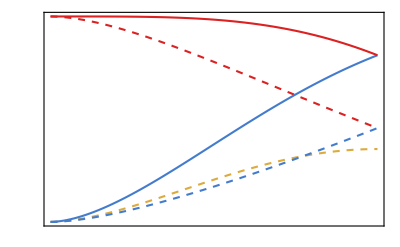

```mathematica
(* generates plot 1 of 3 - Alice's perspective *)
EAon12=Table[{resEC[[;;,1]][[i]],resEC[[;;,2]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
CAon1=Table[{resEC[[;;,1]][[i]],resEC[[;;,3]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
CAon2=Table[{resEC[[;;,1]][[i]],resEC[[;;,4]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
ECAon1=Table[{resEC[[;;,1]][[i]],resEC[[;;,2]][[i]]+resEC[[;;,3]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
ECAon2=Table[{resEC[[;;,1]][[i]],resEC[[;;,2]][[i]]+resEC[[;;,4]][[i]]},{i,1,Length[resEC[[;;,1]]]}];

optionsplot={
PlotRange->{{0,π/4},{Automatic,Automatic}},
PlotStyle->myplotstyle,
Frame->True,
FrameLabel->{MaTeX["(c)~r~(\\mathcal{E}^{(A)},\\mathcal{C}^{(A)})",FontSize->10]},
(*AxesLabel->{MaTeX["r",FontSize->10],MaTeX["",FontSize->10]},*)
PlotLegends->Placed[LineLegend[Automatic,Map[MaTeX[#,FontSize->10]&,{ "\\mathcal{E}_{R,\\bar{R}}^{(A)}","\\mathcal{C}_R^{(A)}","\\mathcal{C}_{\\bar{R}}^{(A)}","\\mathcal{E}_{R,\\bar{R}}^{(A)}+\\mathcal{C}_R^{(A)}","\\mathcal{E}_{R,\\bar{R}}^{(A)}+\\mathcal{C}_{\\bar{R}}^{(A)}"}],LegendMarkerSize->16,Spacings->{0.2,0.01}],{0.19,0.55}],
ImageSize->{246}
};
plot1=ListLinePlot[{EAon12,CAon1,CAon2,ECAon1,ECAon2},optionsplot,FrameTicks->{{vticks,None},{piticks,None}}]
```

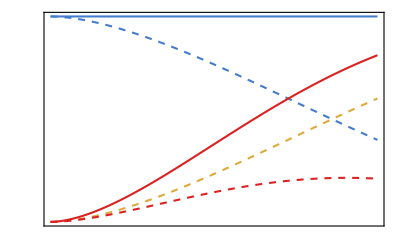

```mathematica
(* generates plot 2 of 3 - Rob's perspective *)
E1onA2=Table[{resEC[[;;,1]][[i]],resEC[[;;,5]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
C1on2=Table[{resEC[[;;,1]][[i]],resEC[[;;,6]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
C1onA=Table[{resEC[[;;,1]][[i]],resEC[[;;,7]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
EC1on2=Table[{resEC[[;;,1]][[i]],resEC[[;;,5]][[i]]+resEC[[;;,6]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
EC1onA=Table[{resEC[[;;,1]][[i]],resEC[[;;,5]][[i]]+resEC[[;;,7]][[i]]},{i,1,Length[resEC[[;;,1]]]}];

optionsplot={
PlotRange->{{0,π/4},{Automatic,Automatic}},
PlotStyle->myplotstyle,
Frame->True,
FrameLabel->{MaTeX["(b)~r~(\\mathcal{E}^{(R)},\\mathcal{C}^{(R)})",FontSize->10]},
(*AxesLabel->{MaTeX["r",FontSize->10],MaTeX["",FontSize->10]},*)
PlotLegends->Placed[LineLegend[Automatic,Map[MaTeX[#,FontSize->10]&,{ "\\mathcal{E}_{A,\\bar{R}}^{(R)}","\\mathcal{C}_{\\bar{R}}^{(R)}","\\mathcal{C}_{A}^{(R)}","\\mathcal{E}_{A,\\bar{R}}^{(R)}+\\mathcal{C}_{\\bar{R}}^{(R)}","\\mathcal{E}_{A,\\bar{R}}^{(R)}+\\mathcal{C}_{A}^{(R)}"}],LegendMarkerSize->16,Spacings->{0.2,0.01}],{0.19,0.55}],
ImageSize->{246}
};
plot2=ListLinePlot[{E1onA2,C1on2,C1onA,EC1on2,EC1onA},optionsplot,FrameTicks->{{vticks,None},{piticks,None}}]
```

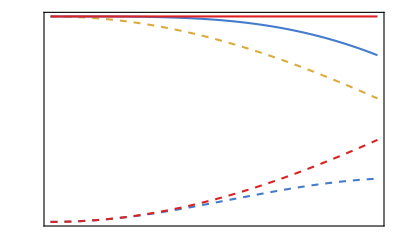

```mathematica
(* generates plot 3 of 3 - anti-Rob's perspective *)
E2onA1=Table[{resEC[[;;,1]][[i]],resEC[[;;,8]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
C2onA=Table[{resEC[[;;,1]][[i]],resEC[[;;,9]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
C2on1=Table[{resEC[[;;,1]][[i]],resEC[[;;,10]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
EC2onA=Table[{resEC[[;;,1]][[i]],resEC[[;;,8]][[i]]+resEC[[;;,9]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
EC2on1=Table[{resEC[[;;,1]][[i]],resEC[[;;,8]][[i]]+resEC[[;;,10]][[i]]},{i,1,Length[resEC[[;;,1]]]}];

optionsplot={
PlotRange->{{0,π/4},{Automatic,Automatic}},
PlotStyle->myplotstyle,
Frame->True,
FrameLabel->{MaTeX["(a)~r~(\\mathcal{E}^{(\\bar{R})},\\mathcal{C}^{(\\bar{R})})",FontSize->10]},
(*AxesLabel->{MaTeX["r",FontSize->10],MaTeX["",FontSize->10]},*)
PlotLegends->Placed[LineLegend[Automatic,Map[MaTeX[#,FontSize->10]&,{ "\\mathcal{E}_{A,R}^{(\\bar{R})}","\\mathcal{C}_{A}^{(\\bar{R})}","\\mathcal{C}_{R}^{(\\bar{R})}","\\mathcal{E}_{A,R}^{(\\bar{R})}+\\mathcal{C}_{A}^{(\\bar{R})}","\\mathcal{E}_{A,R}^{(\\bar{R})}+\\mathcal{C}_{R}^{(\\bar{R})}"}],LegendMarkerSize->16,Spacings->{0.2,0.01}],{0.2,0.55}],
ImageSize->{246}
};
plot3=ListLinePlot[{E2onA1,C2onA,C2on1,EC2onA,EC2on1},optionsplot,FrameTicks->{{vticks,None},{piticks,None}}]
```

```mathematica
(* Save plots *)
Export["EECE100F1.pdf",plot3]
Export["EECE100F2.pdf",plot2]
Export["EECE100F3.pdf",plot1]
```

EECE100F1.pdf

EECE100F2.pdf

EECE100F3.pdf

### Linear Entropy

```mathematica
(* Select values for r and generate data *)
rs=Subdivide[0,π/4,100];
```

```mathematica
(* calculate results in table form *)
resEC={};
Do[
orig=rs[[i]];
val={
N[rs[[i]],10],
N[LinearEntropyR[ρ12,orig],10],
N[L2CoherenceR[ρ12,orig,2],10],
N[L2CoherenceR[ρ12,orig,1],10],
N[LinearEntropyR[ρA2,orig],10],
N[L2CoherenceR[ρA2,orig,1],10],
N[L2CoherenceR[ρA2,orig,2],10],
N[LinearEntropyR[ρA1,orig],10],
N[L2CoherenceR[ρA1,orig,2],10],
N[L2CoherenceR[ρA1,orig,1],10]
};
resEC=Append[resEC,val];
,{i,Length[rs]}]
```

```mathematica
(* Save results - only run if needed *)
Save["LELC100",resEC]
```

```mathematica
(* Import data for plotting *)
resEC=<<"LELC100"; (* ignore this line if you already have resEC defined *)
```

```mathematica
(* preparing the plots *)
cols=ColorData["Rainbow"]/@Subdivide[0,1,4]
tt=AbsoluteThickness[1.5];
myplotstyle={{cols[[4]],Dashed,tt},{cols[[2]],Dashed,tt},{cols[[5]],Dashed,tt},{cols[[2]],tt},{cols[[5]],tt}};
piticks0=Table[{i,i},{i,Range[0,π/4,π/16]}];
piticks0[[;;,2]]=MaTeX[piticks0[[;;,2]],FontSize->10];
piticks=Join[piticks0,Table[{i,"",{0.005,0}},{i,Range[0,π/2,π/64]}]]; 
vticks0={{0,"0.0"},{0.1,"0.1"},{0.2,"0.2"},{0.3,"0.3"},{0.4,"0.4"},{0.5,"0.5"}};
vticks0[[;;,2]]=MaTeX[vticks0[[;;,2]],FontSize->10];
vticks=Join[vticks0,Table[{i,"",{0.005,0}},{i,Range[0,0.5,0.025]}]];
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

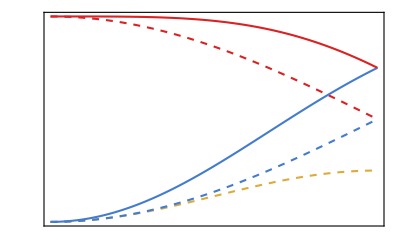

```mathematica
(* generates plot 1 of 3 - Alice's perspective *)
EAon12=Table[{resEC[[;;,1]][[i]],resEC[[;;,2]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
CAon1=Table[{resEC[[;;,1]][[i]],resEC[[;;,3]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
CAon2=Table[{resEC[[;;,1]][[i]],resEC[[;;,4]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
ECAon1=Table[{resEC[[;;,1]][[i]],resEC[[;;,2]][[i]]+resEC[[;;,3]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
ECAon2=Table[{resEC[[;;,1]][[i]],resEC[[;;,2]][[i]]+resEC[[;;,4]][[i]]},{i,1,Length[resEC[[;;,1]]]}];

optionsplot={
PlotRange->{{0,π/4},{Automatic,Automatic}},
PlotStyle->myplotstyle,
Frame->True,
FrameLabel->{MaTeX["(c)~r~(\\mathcal{E}^{(A)},\\mathcal{C}^{(A)})",FontSize->10]},
(*AxesLabel->{MaTeX["r",FontSize->10],MaTeX["",FontSize->10]},*)
PlotLegends->Placed[LineLegend[Automatic,Map[MaTeX[#,FontSize->10]&,{ "\\mathcal{E}_{R,\\bar{R}}^{(A)}","\\mathcal{C}_R^{(A)}","\\mathcal{C}_{\\bar{R}}^{(A)}","\\mathcal{E}_{R,\\bar{R}}^{(A)}+\\mathcal{C}_R^{(A)}","\\mathcal{E}_{R,\\bar{R}}^{(A)}+\\mathcal{C}_{\\bar{R}}^{(A)}"}],LegendMarkerSize->16,Spacings->{0.2,0.01}],{0.19,0.55}],
ImageSize->{246}
};
plot1=ListLinePlot[{EAon12,CAon1,CAon2,ECAon1,ECAon2},optionsplot,FrameTicks->{{vticks,None},{piticks,None}}]
```

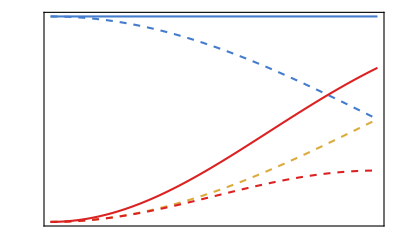

```mathematica
(* generates plot 2 of 3 - Rob's perspective *)
E1onA2=Table[{resEC[[;;,1]][[i]],resEC[[;;,5]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
C1on2=Table[{resEC[[;;,1]][[i]],resEC[[;;,6]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
C1onA=Table[{resEC[[;;,1]][[i]],resEC[[;;,7]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
EC1on2=Table[{resEC[[;;,1]][[i]],resEC[[;;,5]][[i]]+resEC[[;;,6]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
EC1onA=Table[{resEC[[;;,1]][[i]],resEC[[;;,5]][[i]]+resEC[[;;,7]][[i]]},{i,1,Length[resEC[[;;,1]]]}];

optionsplot={
PlotRange->{{0,π/4},{Automatic,Automatic}},
PlotStyle->myplotstyle,
Frame->True,
FrameLabel->{MaTeX["(b)~r~(\\mathcal{E}^{(R)},\\mathcal{C}^{(R)})",FontSize->10]},
(*AxesLabel->{MaTeX["r",FontSize->10],MaTeX["",FontSize->10]},*)
PlotLegends->Placed[LineLegend[Automatic,Map[MaTeX[#,FontSize->10]&,{ "\\mathcal{E}_{A,\\bar{R}}^{(R)}","\\mathcal{C}_{\\bar{R}}^{(R)}","\\mathcal{C}_{A}^{(R)}","\\mathcal{E}_{A,\\bar{R}}^{(R)}+\\mathcal{C}_{\\bar{R}}^{(R)}","\\mathcal{E}_{A,\\bar{R}}^{(R)}+\\mathcal{C}_{A}^{(R)}"}],LegendMarkerSize->16,Spacings->{0.2,0.01}],{0.19,0.55}],
ImageSize->{246}
};
plot2=ListLinePlot[{E1onA2,C1on2,C1onA,EC1on2,EC1onA},optionsplot,FrameTicks->{{vticks,None},{piticks,None}}]
```

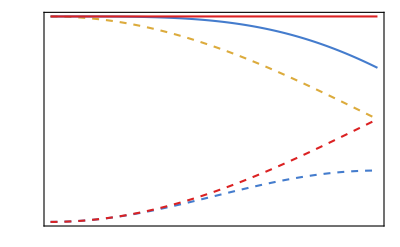

```mathematica
(* generates plot 3 of 3 - anti-Rob's perspective *)
E2onA1=Table[{resEC[[;;,1]][[i]],resEC[[;;,8]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
C2onA=Table[{resEC[[;;,1]][[i]],resEC[[;;,9]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
C2on1=Table[{resEC[[;;,1]][[i]],resEC[[;;,10]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
EC2onA=Table[{resEC[[;;,1]][[i]],resEC[[;;,8]][[i]]+resEC[[;;,9]][[i]]},{i,1,Length[resEC[[;;,1]]]}];
EC2on1=Table[{resEC[[;;,1]][[i]],resEC[[;;,8]][[i]]+resEC[[;;,10]][[i]]},{i,1,Length[resEC[[;;,1]]]}];

optionsplot={
PlotRange->{{0,π/4},{Automatic,Automatic}},
PlotStyle->myplotstyle,
Frame->True,
FrameLabel->{MaTeX["(a)~r~(\\mathcal{E}^{(\\bar{R})},\\mathcal{C}^{(\\bar{R})})",FontSize->10]},
(*AxesLabel->{MaTeX["r",FontSize->10],MaTeX["",FontSize->10]},*)
PlotLegends->Placed[LineLegend[Automatic,Map[MaTeX[#,FontSize->10]&,{ "\\mathcal{E}_{A,R}^{(\\bar{R})}","\\mathcal{C}_{A}^{(\\bar{R})}","\\mathcal{C}_{R}^{(\\bar{R})}","\\mathcal{E}_{A,R}^{(\\bar{R})}+\\mathcal{C}_{A}^{(\\bar{R})}","\\mathcal{E}_{A,R}^{(\\bar{R})}+\\mathcal{C}_{R}^{(\\bar{R})}"}],LegendMarkerSize->16,Spacings->{0.2,0.01}],{0.20,0.55}],
ImageSize->{246}
};
plot3=ListLinePlot[{E2onA1,C2onA,C2on1,EC2onA,EC2on1},optionsplot,FrameTicks->{{vticks,None},{piticks,None}}]
```

```mathematica
(* Save plots *)
Export["LELC100A.pdf",plot1]
Export["LELC100R.pdf",plot2]
Export["LELC100Rbar.pdf",plot3]
```

LELC100A.pdf

LELC100R.pdf

LELC100Rbar.pdf

## Analytic Expressions and Comparisons

For this part, you need to run ‘Density Matrices’ and ‘Main Functions’ subsections (see above).

```mathematica
(* Three qubit state from Alsing 2006 *)
Psi={{1/(√2)Cos[r]},{0},{0},{1/(√2)Sin[r]},{0},{0},{1/(√2)},{0}};
Psi//MatrixForm
```

(Cos[r]/(√2)
0
0
Sin[r]/(√2)
0
0
1/(√2)
0)

```mathematica
Rho=Psi.Transpose[Psi];
Rho//MatrixForm
```

(Cos[r]^2/2 | 0 | 0 | 1/2 Cos[r] Sin[r] | 0 | 0 | Cos[r]/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 Cos[r] Sin[r] | 0 | 0 | Sin[r]^2/2 | 0 | 0 | Sin[r]/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Cos[r]/2 | 0 | 0 | Sin[r]/2 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Helper Functions

```mathematica
(* New definitions of entanglement entropy that takes in an N-qubit density matrix and traces out the s^th system *)
EntanglementEntropy[ρ_,rr_,s_]:=Module[{ρR,ρPT,λPT,EE},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
λPT=Eigenvalues[ρPT];
EE=Sum[-λPT[[i]]*Log2[λPT[[i]]],{i,1,Length[λPT]}];
Return[EE]];

LinearEntropy[ρ_,rr_,s_]:=Module[{ρR,ρPT},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
Return[1-Tr[MatrixPower[ρPT,2]]]];

(* Computes ρ-tilde for a 2-qubit density matrix ρ *)
(* Ignores conjugate because ρ only has real elements *)
SpinFlip[ρ_]:=KroneckerProduct[({{0, -I}, {I, 0}}),({{0, -I}, {I, 0}})].ρ.KroneckerProduct[({{0, -I}, {I, 0}}),({{0, -I}, {I, 0}})];

(* M(ρ), as defined underneath Eq. (30) in Alsing 2006 *)
MFn[ρ_]:=1-Tr[MatrixPower[ρ,2]];

(* η(ρ), as defined in Eq. (30) in Alsing 2006 *)
(* ρ is a pure 3-qubit state, s^th system traced out *)
(* The tangle appears to be just concurrence, not concurrence squared, as written on Page 11 *)
Eta[ρ_,rr_,s_]:=Module[{ρR,ρPT,ρTilde,λTilde,CC},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
ρTilde=SpinFlip[ρPT];
λTilde=ReverseSort[Eigenvalues[ρPT.ρTilde]];
CC=Simplify[Max[0,λTilde[[1]]-λTilde[[2]]-λTilde[[3]]-λTilde[[4]]],{0<=r<=π/4}];
Return[Tr[ρPT.ρTilde]+MFn[ρPT]-CC]];

(* From the 3-qubit state, traces out one of the systems, then calculates concurrence for the remaining bipartite state *)
Concurrence[ρ_,rr_,s_]:=Module[{ρR,ρPT,ρTilde,λTilde,CC},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
ρTilde=SpinFlip[ρPT];
λTilde=ReverseSort[Eigenvalues[ρPT.ρTilde]];
CC=Simplify[Max[0,λTilde[[1]]-λTilde[[2]]-λTilde[[3]]-λTilde[[4]]],{0<=r<=π/4}];
Return[CC]];

(* From the 3-qubit state, traces out one of the systems, then calculates entanglement of formation for the remaining bipartite state *)
(* As with the tangle, the expression appears to work for C rather than C^2 *)
EntanglementOfFormation[ρ_,rr_,s_]:=Module[{ρR,ρPT,ρTilde,λTilde,CC,EF},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
ρTilde=SpinFlip[ρPT];
λTilde=ReverseSort[Eigenvalues[ρPT.ρTilde]];
CC=Simplify[Max[0,λTilde[[1]]-λTilde[[2]]-λTilde[[3]]-λTilde[[4]]],{0<=r<=π/4}];
EF=-(1+√(1-CC))/2 Log[2,(1+√(1-CC))/2]-(1-√(1-CC))/2 Log[2,(1-√(1-CC))/2];
Return[EF]];

(* Computes partial transpose for a 2-qubit density matrix, transposes 2nd system *)
(* Credit: kglr on Mathematica StackExchange *)
(* https://mathematica.stackexchange.com/questions/221273/partial-transpose-of-8x8-density-matrix *)
PartialTranspose[ρ_]:=Module[{ρP,PT},
ρP=Partition[ρ,{2,2}];
PT=ArrayFlatten@Map[Transpose,#,{2}]&;
Return[PT@ρP]];

(* From the 3-qubit state, traces out one of the systems, then calculates logarithmic negativity for the remaining bipartite state *)
(* Assumes ρ is real and symmetric, otherwise the function is more general *)
LogarithmicNegativity[ρ_,rr_,s_]:=Module[{ρR,ρPT,ρPTT,λPTT,TN},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
ρPTT=PartialTranspose[ρPT];
λPTT=Eigenvalues[ρPTT];
TN=Sum[RealAbs[λPTT[[i]]],{i,Length[λPTT]}];
Return[Log2[TN]]];

(* Calculates the Von Neumann entropy for a state ρ *)
VonNeumannEntropy[ρ_]:=Module[{λ},
λ=Eigenvalues[ρ];
Return[Sum[-λ[[i]]*Log2[λ[[i]]],{i,Length[λ]}]]];

(* Calculates mutual information for a specified pair of systems *)
(* Doesn't yield Fig 5... *)
MutualInformation[ρ_,rr_,s_]:=Module[{ρR,ρPT,ρPT1,ρPT2},
ρR=ρ /. {r->rr};
ρPT=TraceSystem[ρR,{s}];
ρPT1=TraceSystem[ρPT,{2}];
ρPT2=TraceSystem[ρPT,{1}];
Return[VonNeumannEntropy[ρPT1]+VonNeumannEntropy[ρPT2]-VonNeumannEntropy[ρPT]]];
```

### Expressions for Entanglement Entropy and Entropy of Coherence

```mathematica
(* Entanglement entropy, Alice's perspective *)
(* All logs are base 2; for some reason, Mathematica doesn't simplify these *)
EntanglementEntropyR[ρ12,r]
```

((-4+√2 √(7+Cos[4 r])) Log[1/8 (4-√2 √(7+Cos[4 r]))])/(8 Log[2])+((-4-√2 √(7+Cos[4 r])) Log[1/8 (4+√2 √(7+Cos[4 r]))])/(8 Log[2])

```mathematica
(* Rob's subsystem entropy of coherence, Alice's perspective *)
Simplify[EntropyOfCoherenceR[ρ12,r,2]]
```

-1/(8 Log[2])(2 (3+Cos[2 r]) Log[1/4 (3+Cos[2 r])]+(-4+√2 √(7+Cos[4 r])) Log[1/8 (4-√2 √(7+Cos[4 r]))]-(4+√2 √(7+Cos[4 r])) Log[1/8 (4+√2 √(7+Cos[4 r]))]+4 Log[Sin[r]^2/2] Sin[r]^2)

```mathematica
(* Anti-Rob's subsystem entropy of coherence, Alice's perspective *)
Simplify[EntropyOfCoherenceR[ρ12,r,1]]
```

1/(8 Log[2])(-4 Cos[r]^2 Log[Cos[r]^2/2]-(-4+√2 √(7+Cos[4 r])) Log[1/8 (4-√2 √(7+Cos[4 r]))]+(4+√2 √(7+Cos[4 r])) Log[1/8 (4+√2 √(7+Cos[4 r]))]+2 (-3+Cos[2 r]) Log[1/2 (1+Sin[r]^2)])

```mathematica
(* Entanglement entropy, Rob's perspective *)
EntanglementEntropyR[ρA2,r]
```

((-1+Cos[r]) Log[1/2 (1-Cos[r])])/(2 Log[2])+((-1-Cos[r]) Log[1/2 (1+Cos[r])])/(2 Log[2])

```mathematica
(* Alice's subsystem entropy of coherence, Rob's perspective *)
EntropyOfCoherenceR[ρA2,r,2]
```

-((-1+Cos[r]) Log[1/2 (1-Cos[r])])/(2 Log[2])-((-1-Cos[r]) Log[1/2 (1+Cos[r])])/(2 Log[2])+((-1/2-Cos[r]^2/2) Log[1/2+Cos[r]^2/2])/Log[2]-(Log[Sin[r]^2/2] Sin[r]^2)/(2 Log[2])

```mathematica
(* Anti-Rob's subsystem entropy of coherence, Rob's perspective *)
EntropyOfCoherenceR[ρA2,r,1]
```

1/2-((-1+Cos[r]) Log[1/2 (1-Cos[r])])/(2 Log[2])-((-1-Cos[r]) Log[1/2 (1+Cos[r])])/(2 Log[2])+(Log[Cos[r]^2/2+Sin[r]^2/2] (-1/2 Cos[r]^2-Sin[r]^2/2))/Log[2]

```mathematica
(* Entanglement entropy, anti-Rob's perspective *)
EntanglementEntropyR[ρA1,r]
```

(Log[1/2 (1+Sin[r])] (-1-Sin[r]))/(2 Log[2])+(Log[1/2 (1-Sin[r])] (-1+Sin[r]))/(2 Log[2])

```mathematica
(* Alice's subsystem entropy of coherence, anti-Rob's perspective *)
EntropyOfCoherenceR[ρA1,r,2]
```

-(Cos[r]^2 Log[Cos[r]^2/2])/(2 Log[2])-(Log[1/2 (1+Sin[r])] (-1-Sin[r]))/(2 Log[2])-(Log[1/2 (1-Sin[r])] (-1+Sin[r]))/(2 Log[2])+(Log[1/2+Sin[r]^2/2] (-1/2-Sin[r]^2/2))/Log[2]

```mathematica
(* Rob's subsystem entropy of coherence, anti-Rob's perspective *)
EntropyOfCoherenceR[ρA1,r,1]
```

1/2-(Log[1/2 (1+Sin[r])] (-1-Sin[r]))/(2 Log[2])-(Log[1/2 (1-Sin[r])] (-1+Sin[r]))/(2 Log[2])+(Log[Cos[r]^2/2+Sin[r]^2/2] (-1/2 Cos[r]^2-Sin[r]^2/2))/Log[2]

### Expressions for Linear Entropy and L2-Norm of Coherence

```mathematica
(* Linear entropy, Alice's perspective *)
LinearEntropyR[ρ12,r]//FullSimplify
```

1/8 Sin[2 r]^2

```mathematica
(* Rob's subsystem L2-norm of coherence, Alice's perspective *)
(* Note that r is real, so the absolute value goes away *)
L2CoherenceR[ρ12,r,2]
```

1/2 Abs[Sin[r]]^2

```mathematica
(* Anti-Rob's subsystem L2-norm of coherence, Alice's perspective *)
L2CoherenceR[ρ12,r,1]
```

1/2 Abs[Cos[r]]^2

```mathematica
(* Linear entropy, Rob's perspective *)
LinearEntropyR[ρA2,r]//FullSimplify
```

Sin[r]^2/2

```mathematica
(* Alice's subsystem L2-norm of coherence, Rob's perspective *)
L2CoherenceR[ρA2,r,2]
```

1/2 Abs[Cos[r] Sin[r]]^2

```mathematica
(* Anti-Rob's subsystem L2-norm of coherence, Rob's perspective *)
L2CoherenceR[ρA2,r,1]
```

1/2 Abs[Cos[r]]^2

```mathematica
(* Linear entropy, anti-Rob's perspective *)
LinearEntropyR[ρA1,r]//FullSimplify
```

Cos[r]^2/2

```mathematica
(* Alice's subsystem L2-norm of coherence, anti-Rob's perspective *)
L2CoherenceR[ρA1,r,2]
```

1/2 Abs[Cos[r] Sin[r]]^2

```mathematica
(* Rob's subsystem L2-norm of coherence, anti-Rob's perspective *)
L2CoherenceR[ρA1,r,1]
```

1/2 Abs[Sin[r]]^2

### Check if Linear Entropy for Alsing 2006 also Matches E+C

```mathematica
(* Linear entropy, tracing out Alice's system *)
(* A good sign: this always equals 1/2 *)
LinearEntropy[Rho,r,1]//FullSimplify
```

1/2

```mathematica
(* Linear entropy, tracing out Rob's system *)
LinearEntropy[Rho,r,2]//FullSimplify
```

-1/4 Cos[r]^2 (-3+Cos[2 r])

```mathematica
(* Linear entropy, tracing out anti-Rob's system *)
LinearEntropy[Rho,r,3]//FullSimplify
```

1/4 (3+Cos[2 r]) Sin[r]^2

```mathematica
(* Here I define the two non-trivial functions out of the three calculated directly above *)
(* Note that I have simplified the expressions *)
L1[r_]:=Cos[r]^2(1-Cos[r]^2/2);
L2[r_]:=Sin[r]^2/2(1+Cos[r]^2);
```

```mathematica
(* Plotting *)
rs=Subdivide[0,π/4,100];
```

```mathematica
L1res=Table[{rs[[i]],L1[rs[[i]]]},{i,Length[rs]}];
L2res=Table[{rs[[i]],L2[rs[[i]]]},{i,Length[rs]}];
```

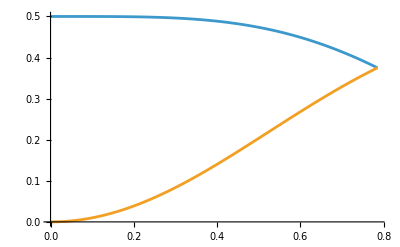

```mathematica
ListLinePlot[{L1res,L2res}]
```

```mathematica
(* Reading in the numerical data that was generated for the E+C problem *)
resEC=<<"LELC100";
```

```mathematica
res1=Table[{resEC[[;;,1]][[i]],resEC[[;;,2]][[i]]+resEC[[;;,4]][[i]]},{i,Length[resEC]}];res2=Table[{resEC[[;;,1]][[i]],resEC[[;;,2]][[i]]+resEC[[;;,3]][[i]]},{i,Length[resEC]}];
```

```mathematica
ListLinePlot[{res1,res2}]
```

-Graphics-

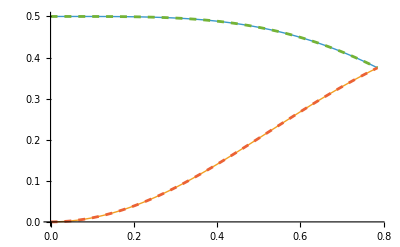

```mathematica
(* direct comparison of all four curves *)
ListLinePlot[{L1res,L2res,res1,res2},PlotStyle->{Thick,Thick,Dashed,Dashed}]
```

```mathematica
(* Numerical checks - these should be 0 *)
Simplify[LinearEntropyR[ρ12,r]+L2CoherenceR[ρ12,r,2]-Sin[r]^2/2(1+Cos[r]^2),Element[r, Reals]]
```

0

```mathematica
Simplify[LinearEntropyR[ρ12,r]+L2CoherenceR[ρ12,r,1]-Cos[r]^2(1-Cos[r]^2/2),Element[r, Reals]]
```

0

### Alsing 2006 Fig 7 Comparison with E+C

```mathematica
(* Separable uncertainty η(ρ), tracing out Alice *)
(* Nice to find that this is always 1/2 *)
Eta[Rho,r,1]//FullSimplify
```

1/2

```mathematica
(* Separable uncertainty η(ρ), tracing out Rob *)
Eta[Rho,r,2]//FullSimplify
```

-1/4 Cos[r]^2 (-3+Cos[2 r])

```mathematica
(* Linear entropy, tracing out Rob's system *)
(* Observe that this is identical to the above! *)
LinearEntropy[Rho,r,2]//FullSimplify
```

-1/4 Cos[r]^2 (-3+Cos[2 r])

```mathematica
(* Separable uncertainty η(ρ), tracing out anti-Rob *)
Eta[Rho,r,3]//FullSimplify
```

1/4 (3+Cos[2 r]) Sin[r]^2

```mathematica
(* Linear entropy, tracing out anti-Rob's system *)
(* Again, identical! *)
LinearEntropy[Rho,r,3]//FullSimplify
```

1/4 (3+Cos[2 r]) Sin[r]^2

Conclusion: Fig 7 in Alsing 2006 is identical to E+C in Fig 2 of our paper (linear entropy plus l2-norm of coherence)!

```mathematica
(* Plotting η(ρ) *)
rs=Subdivide[0,π/4,100];
```

```mathematica
Eta1res=Table[{rs[[i]],Eta[Rho,rs[[i]],1]},{i,Length[rs]}];
Eta2res=Table[{rs[[i]],Eta[Rho,rs[[i]],2]},{i,Length[rs]}];
Eta3res=Table[{rs[[i]],Eta[Rho,rs[[i]],3]},{i,Length[rs]}];
```

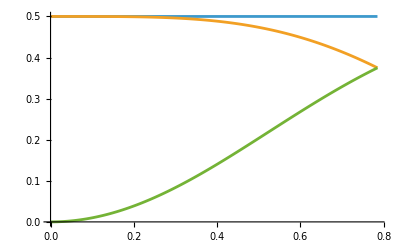

```mathematica
ListLinePlot[{Eta1res,Eta2res,Eta3res}]
```

Plotting the concurrence reproduces Fig 6 in Alsing 2006.

```mathematica
(* Plotting C(ρ) *)
rs=Subdivide[0,π/4,100];
```

```mathematica
C1res=Table[{rs[[i]],Concurrence[Rho,rs[[i]],1]},{i,Length[rs]}];
C2res=Table[{rs[[i]],Concurrence[Rho,rs[[i]],2]},{i,Length[rs]}];
C3res=Table[{rs[[i]],Concurrence[Rho,rs[[i]],3]},{i,Length[rs]}];
```

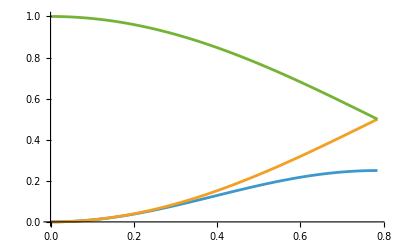

```mathematica
ListLinePlot[{C1res,C2res,C3res}]
```

### Reproduction of Figures 2-7 in Alsing 2006

```mathematica
rs=Subdivide[0,π/4,100];
```

#### Figure 2

```mathematica
(* Bipartite entanglement *)
BE1res=Table[{rs[[i]],EntanglementEntropy[Rho,rs[[i]],1]},{i,Length[rs]}];
BE2res=Table[{rs[[i]],EntanglementEntropy[Rho,rs[[i]],2]},{i,Length[rs]}];
BE3res=Table[{rs[[i]],EntanglementEntropy[Rho,rs[[i]],3]},{i,Length[rs]}];
```

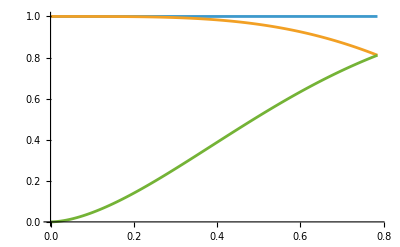

```mathematica
ListLinePlot[{BE1res,BE2res,BE3res}]
```

#### Figure 3

```mathematica
(* Logarithmic negativity *)
```

```mathematica
LN1res=Table[{rs[[i]],LogarithmicNegativity[Rho,rs[[i]],1]},{i,Length[rs]}];
LN2res=Table[{rs[[i]],LogarithmicNegativity[Rho,rs[[i]],2]},{i,Length[rs]}];
LN3res=Table[{rs[[i]],LogarithmicNegativity[Rho,rs[[i]],3]},{i,Length[rs]}];
```

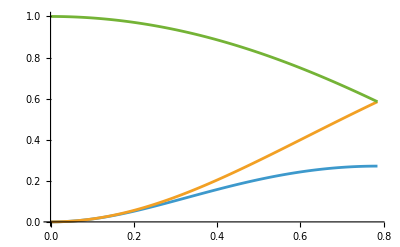

```mathematica
ListLinePlot[{LN1res,LN2res,LN3res}]
```

#### Figure 4

```mathematica
(* Entanglement of formation *)
EF1res=Table[{rs[[i]],EntanglementOfFormation[Rho,rs[[i]],1]},{i,Length[rs]}];
EF2res=Table[{rs[[i]],EntanglementOfFormation[Rho,rs[[i]],2]},{i,Length[rs]}];
EF3res=Table[{rs[[i]],EntanglementOfFormation[Rho,rs[[i]],3]},{i,Length[rs]}];
```

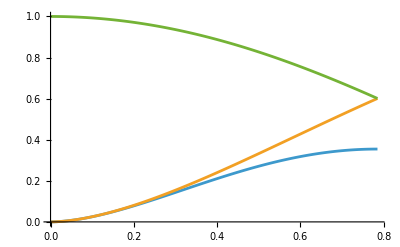

```mathematica
ListLinePlot[{EF1res,EF2res,EF3res}]
```

```mathematica
(* Perspectival entanglement entropy *)
E1res=Table[{rs[[i]],EntanglementEntropyR[ρ12,rs[[i]]]},{i,Length[rs]}];
E2res=Table[{rs[[i]],EntanglementEntropyR[ρA2,rs[[i]]]},{i,Length[rs]}];
E3res=Table[{rs[[i]],EntanglementEntropyR[ρA1,rs[[i]]]},{i,Length[rs]}];
f[r_]:=-1/2(1+√((7+Cos[4r])/□))
```

```mathematica
ListLinePlot[{E1res,E2res,E3res}]
```

-Graphics-

#### Figure 5

```mathematica
(* Mutual information - not quite reproducing as expected *)
MI1res=Table[{rs[[i]],MutualInformation[Rho,rs[[i]],1]},{i,Length[rs]}];
MI2res=Table[{rs[[i]],MutualInformation[Rho,rs[[i]],2]},{i,Length[rs]}];
MI3res=Table[{rs[[i]],MutualInformation[Rho,rs[[i]],3]},{i,Length[rs]}];
```

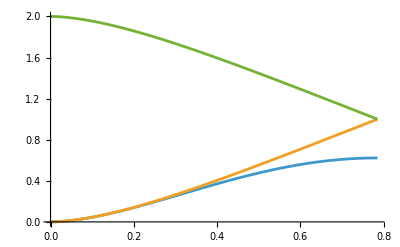

```mathematica
ListLinePlot[{MI1res,MI2res,MI3res}]
```

```mathematica
(* Mutual information in perspectival case, equals twice entanglement entropy *)
MI1p=Table[{rs[[i]],2*EntanglementEntropy[ρ12,rs[[i]],2]},{i,Length[rs]}];
MI2p=Table[{rs[[i]],2*EntanglementEntropy[ρA2,rs[[i]],2]},{i,Length[rs]}];
MI3p=Table[{rs[[i]],2*EntanglementEntropy[ρA1,rs[[i]],2]},{i,Length[rs]}];
```

```mathematica
(* Plotting mutual info vs perspectival mutual info *)
cols=ColorData["Rainbow"]/@Subdivide[0,1,4]
tt=AbsoluteThickness[1.5];
myplotstyle={{cols[[4]],tt},{cols[[4]],Dashed,tt},{cols[[2]],tt},{cols[[2]],Dashed,tt},{cols[[1]],tt},{cols[[1]],Dashed,tt}};
piticks0=Table[{i,i},{i,Range[0,π/4,π/16]}];
piticks0[[;;,2]]=MaTeX[piticks0[[;;,2]],FontSize->10];
piticks=Join[piticks0,Table[{i,"",{0.005,0}},{i,Range[0,π/2,π/64]}]]; 
vticks0={{0,"0.0"},{0.4,"0.4"},{0.8,"0.8"},{1.2,"1.2"},{1.6,"1.6"},{2,"2.0"}};
vticks0[[;;,2]]=MaTeX[vticks0[[;;,2]],FontSize->10];
vticks=Join[vticks0,Table[{i,"",{0.005,0}},{i,Range[0,2,0.1]}]];
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
optionsplot={
PlotRange->{{0,π/4},{Automatic,Automatic}},
PlotStyle->myplotstyle,
Frame->True,
FrameLabel->{MaTeX["r",FontSize->10]},
(*AxesLabel->{MaTeX["r",FontSize->10],MaTeX["",FontSize->10]},*)
PlotLegends->Placed[LineLegend[Automatic,Map[MaTeX[#,FontSize->10]&,{ "\\mathcal{I}_{R,\\bar{R}}","\\mathcal{I}_{R,\\bar{R}}^{(A)}","\\mathcal{I}_{A,\\bar{R}}","\\mathcal{I}_{A,\\bar{R}}^{(R)}","\\mathcal{I}_{A,R}","\\mathcal{I}_{A,R}^{(\\bar{R})}"}],LegendMarkerSize->16,Spacings->{0.2,0.01}],{0.15,0.51}],
ImageSize->{246}
};
```

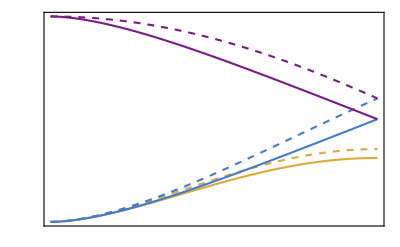

```mathematica
plotMI=ListLinePlot[{MI1res,MI1p,MI2res,MI2p,MI3res,MI3p},optionsplot,FrameTicks->{{vticks,None},{piticks,None}}]
```

```mathematica
Export["MI100.pdf",plotMI]
```

MI100.pdf

```mathematica
N[3/2*(2-Log2[3])]
```

0.622556

```mathematica
N[-(1+1/(√2))*Log2[1/2+1/(2 √2)]-(1-1/(√2))*Log2[1/2-1/(2 √2)]]
```

1.20175

#### Figure 6

```mathematica
(* Concurrence *)
C1res=Table[{rs[[i]],Concurrence[Rho,rs[[i]],1]},{i,Length[rs]}];
C2res=Table[{rs[[i]],Concurrence[Rho,rs[[i]],2]},{i,Length[rs]}];
C3res=Table[{rs[[i]],Concurrence[Rho,rs[[i]],3]},{i,Length[rs]}];
```

```mathematica
ListLinePlot[{C1res,C2res,C3res}]
```

-Graphics-

#### Figure 7

```mathematica
(* Separable uncertainty *)
SU1res=Table[{rs[[i]],Eta[Rho,rs[[i]],1]},{i,Length[rs]}];
SU2res=Table[{rs[[i]],Eta[Rho,rs[[i]],2]},{i,Length[rs]}];
SU3res=Table[{rs[[i]],Eta[Rho,rs[[i]],3]},{i,Length[rs]}];
```

```mathematica
ListLinePlot[{SU1res,SU2res,SU3res}]
```

-Graphics-